# Wilson-Fisher fixed-points for O(n)-models in d=3 from the Wetterich equation

implemented by Michael M. Scherer

This simple mathematica-.nb allows to compute critical exponents of three-dimensional bosonic O(n)-models from a functional renormalization group approach based on the Wetterich equation.

In order to start the evaluation specify n in the cell "Input parameters". Then press “shift+enter” with the cursor in the cell below “Stability matrix and critical exponents” and confirm to automatically evaluate all the initialisation cells. Also specify computation in leading order derivative expansion or next-to-leading order inlcuding a running wave function renormalization. The results for leading order have been checked for n>0 to be consistent with “Critical exponents from optimised renormalisation group flows” by Daniel Litim, Nucl. Phys. B 631, 128-158 (2002). Basics about the functional RG approach used here and about the notation can be found in “Non-Perturbative Renormalization Flow in Quantum Field Theory and Statistical Physics” by J. Berges, Nikolaos Tetradis, and C. Wetterich, Phys. Rept. 363:223-386 (2002).

## Input parameters

```mathematica
dd=3;
n=2; (* Number of field components *)
λmax=6; (* Expansion order of the effective potential Subscript[u, eff]=Subscript[Σ, i=2] Subscript[λ, i]/(i!)(ρ-Subscript[λ, 1])^i. *)
NLO=1; (* Set NLO = 0 to compute without anomalous dimension Subscript[η, ϕ], set NLO = 1 to include anomalous dimension *)
```

## Flow equations & truncation

### Flow equation for the effective potential and the anomalous dimension in d dimensions

```mathematica
dtu[d_]:=-d u[ρ]+(d-2+ηϕ[d])ρ u'[ρ]+I0[d,u'[ρ]+2 ρ u''[ρ]]+(n-1)I0[d,u'[ρ]] (* flow equation for the effective potential *)
ηϕ[d_]:=If[NLO==1,(16 vd[d])/d λ[1](λ[2])^2 m[2λ[1]λ[2]],0] (* anomalous dimension *)
```

#### Volume factor and threshold functions

```mathematica
vd[d_]:=(Gamma[d/2] 2^(d+1)π^(d/2))^-1 (* volume factor *)
I0Litim[d_,ω_]:=(4vd[d])/d(1-ηϕ[d]/(d+2))1/(1+ω) (* threshold function for the effective potential *)
I0sc[d_,ω_]:=-2vd[d]Log[(1+ω)] (* threshold function for the effective potential *)

I0[d_,ω_]:=I0Litim[d,ω];
m[ω_]:=1/(1+ω)^2 (* threshold function for the anomalous dimension *)
```

### Projection on the flow of the running couplings for d=3

```mathematica
dtλ1:= D[-dtu[dd]/λ[2],ρ] (* Flow of the minimum of the effective potential *)
dtλ[ord_]:=(D[dtu[dd],{ρ,ord}]+Derivative[ord+1][u][ρ] dtλ1) (* Flow of the couplings of the effective potential *)
```

### Fixed point equations

```mathematica
Off[FindRoot::jsing]
SSB:={u'[ρ]->0,ρ->λ[1],u''[ρ]->λ[2]}; (* Evaluate effective potential at minimum *)
λExp[n1_]:=Table[Derivative[i][u][λ[1]]->λ[i],{i,3,n1+2}]/.{λ[n1+1]->0,λ[n1+2]->0} (* introduce notation for couplings *)

βfunc[n2_]:=Append[Table[dtλ[i]==0,{i,2,n2}],dtλ1==0]//.SSB//.λExp[n2]
fp[2]=FindRoot[βfunc[2],{{λ[1],0.01},{λ[2],6}},WorkingPrecision->20];
fp[n3_]:=FindRoot[βfunc[n3],Append[Table[{λ[i],λ[i]/.fp[n3-1]},{i,1,n3-1}],{λ[n3],10^(n3-1)}],WorkingPrecision->20];
Do[fp[i],{i,2,λmax,1}]
```

## Stability matrix and critical exponents

```mathematica
βlist[n5_]:=Flatten[{dtλ1,Table[dtλ[i],{i,2,n5}]}]//.SSB//.λExp[n5]
sm[n6_,i_,j_]:=D[βlist[n6][[i]],j]
StabilityMatrix[n7_]:=Table[sm[n7,j,λ[i]],{i,1,n7},{j,1,n7}]//.fp[n7]
smEigVal[n8_]:=Sort[-Re[N[Eigenvalues[StabilityMatrix[n8]]]],Greater]
νlist={};Do[ν=1/(smEigVal[n9][[1]]);Subscript[ω, 2]=-smEigVal[n9][[2]];Subscript[η, ϕ]=ηϕ[3]//.fp[n9];νlist=Append[νlist,{n9,ν}];
Print["n=",NumberForm[n,3],", λ_max=",Subscript[λ, n9],", θ_1=",NumberForm[smEigVal[n9][[1]],3],", ν=",NumberForm[ν,3],", ω=",NumberForm[Subscript[ω, 2],3], ", η_ϕ=",NumberForm[Re[Subscript[η, ϕ]],6]],{n9,2,λmax,1}]
```

n=2, λ_max=λ_2, θ_1=1.66, ν=0.604, ω=0.518, η_ϕ=0.0593267

n=2, λ_max=λ_3, θ_1=1.4, ν=0.716, ω=1.12, η_ϕ=0.0391512

n=2, λ_max=λ_4, θ_1=1.45, ν=0.691, ω=0.719, η_ϕ=0.0433951

n=2, λ_max=λ_5, θ_1=1.46, ν=0.685, ω=0.722, η_ϕ=0.0438615

n=2, λ_max=λ_6, θ_1=1.46, ν=0.685, ω=0.735, η_ϕ=0.0437319

## Flow to scaling solution for ϕ^8-truncation

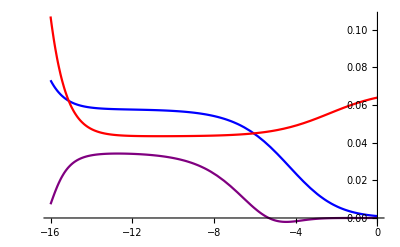

```mathematica
βfunction[n5_]:=Flatten[{dtλ1,Table[dtλ[i],{i,2,n5}]}]//.SSB//.λExp[n5]
βruns=Simplify[βfunction[4]/.{λ[1]->κ[t],λ[2]->λ2[t],λ[3]->λ3[t],λ[4]->λ4[t]}];

i=0;tno=0;interval=0;sign=1;κinit=0.12;tIR=-16;

While[tno>tIR,interval=interval+sign(1/2)^i;κin=0.1*interval;
solBase=NDSolve[{κ'[t]==βruns[[1]],λ2'[t]==βruns[[2]],λ3'[t]==βruns[[3]],λ4'[t]==βruns[[4]],κ[0]==κin,λ2[0]==0.1,λ3[0]==0,λ4[0]==0},{κ,λ2,λ3,λ4},{t,0,tIR},StoppingTest:>Re[κ[t]]<(0.9*λ[1]/.fp[2])||(Re[κ[t]])>κinit];
tno=solBase⟦1,1,2,1,1,1⟧;
sign=If[(κ[tno]/.solBase)[[1]]>κin,-1,1];i++]
Plot[{λ2[t]/100/.solBase,λ4[t]/10000/.solBase,κ[t]/.solBase},{t,0,tno},PlotStyle->{Blue,Purple,Red},AxesOrigin->{0,0}]
```